### Installer function definitions

```mathematica
copier[basedir_,file_]:=
If[
FileNames[ToFileName[{basedir,"Applications"},file]]=={} ||
(ChoiceDialog[TextCell["Destination file exists. Replace it?","Subsubsection"]]
&& DeleteFile[ToFileName[{basedir,"Applications"},file]]=!=$Failed),

CopyFile[ToFileName[NotebookDirectory[],file],ToFileName[{basedir,"Applications"},file]],
$Failed
]
```

```mathematica
installpackage[name_]:=
Block[{dir},
If[
(dir=ChoiceDialog[TextCell["Install the ErrorBarLogPlots package?","Subsubsection"],
{"For all users"->$BaseDirectory,"For just you"->$UserBaseDirectory,
"Cancel"->$Canceled}])=!=$Canceled,
If[copier[dir,name]=!= $Failed,
DialogInput[Column[{TextCell["Package installed.","Subsubsection"],
DefaultButton["OK",DialogReturn[True]]}]],
DialogInput[Column[{TextCell["Installation failed!","Subsubsection"],
DefaultButton["OK",DialogReturn[True]]}]]
];
]
]
```

### Run Installer

```mathematica
installpackage["ErrorBarLogPlots.m"];
```

## Using the package :

```mathematica
Needs["ErrorBarLogPlots`"]
```

## The functions just installed :

```mathematica
?ErrorListLog*
```

```mathematica
?ErrorListLogPlot
```

ErrorListLogPlot[{{y_1,dy_1},{y_2,dy_2},…}] makes a log plot of points corresponding to a list of values y_1, y_2, …, with corresponding error bars. The errors have magnitudes dy_1,dy_2,….
ErrorListLogPlot[{{{x_1,y_1},ErrorBar[err_1]},{{x_2,y_2},ErrorBar[err_2]},…}] makes a log plot of points with specified x and y coordinates and error magnitudes.

```mathematica
?ErrorBarScale
```

ErrorBarScale[] can be supplied as a value for the ErrorBarFunction option of the ErrorListPlot family. It scales error bar sizes to make them more visible in a plot.
ErrorBarFunction→ErrorBarScale[scale] scale factor scale is applied to error bars in both the x and y directions
ErrorBarFunction→ErrorBarScale[xscale,yscale] scale factors specified independently for each of the x and the y error bars

```mathematica
?ErrorBar
```

ErrorBar[{negerror,poserror}] represents error in the positive and negative directions.
ErrorBar[yerr] represents error yerr in both the positive and negative directions.
ErrorBar[xerr,yerr] represents errors specified for both the x and the y coordinates.

## Some example plots :

### Compare ErrorListLogLogPlot to ListLogLogPlot :

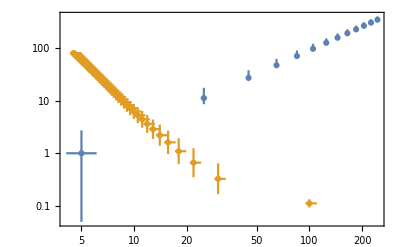

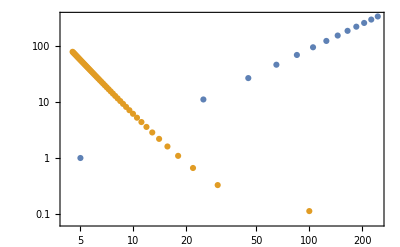

```mathematica
ErrorListLogLogPlot[
{
Table[{{5 i,i^1.5},ErrorBar[ 1,    {-3,i}]},{i,1,50,4}],
Table[{{10/i^.5,i+5i^1.7+.1},ErrorBar[{-.5, 1}/i^.5,    2i]},{i,.01,5,.1}]
},
ImageSize->400,
Frame->True,Axes->False,
GridLines->Automatic,GridLinesStyle->GrayLevel[.9]
]

ListLogLogPlot[
{
Table[{5 i,i^1.5},{i,1,50,4}],
Table[{10/i^.5,i+5i^1.7+.1},{i,.01,5,.1}]
},
ImageSize->400,
Frame->True,Axes->False,
GridLines->Automatic,GridLinesStyle->GrayLevel[.9]
]
```

### Using ErrorBarScale :

#### An actual data set of a resonant response - errordata

```mathematica
errordata={{{15319.23,28.90412},ErrorBar[0.1025415,0.09526304]},{{15328.44,29.96474},ErrorBar[0.1245095,0.08365633]},{{15338.45,31.09912},ErrorBar[0.09531945,0.05792714]},{{15348.72,32.2629},ErrorBar[0.0874754,0.1008571]},{{15357.9,33.62319},ErrorBar[0.115113,0.1132482]},{{15367.09,35.04674},ErrorBar[0.08765405,0.1083145]},{{15378.04,36.60379},ErrorBar[0.05373801,0.1323072]},{{15387.28,38.44707},ErrorBar[0.09646767,0.3394694]},{{15396.69,40.0524},ErrorBar[0.100941,0.2613853]},{{15406.3,42.13074},ErrorBar[0.1452327,0.2994218]},{{15415.02,44.68117},ErrorBar[0.108216,0.2905232]},{{15424.82,47.01453},ErrorBar[0.1066591,0.3666612]},{{15435.64,49.60391},ErrorBar[0.07954776,0.4403643]},{{15445.33,52.414},ErrorBar[0.1398945,0.4166706]},{{15454.55,56.01776},ErrorBar[0.135189,0.5917878]},{{15464.63,59.37961},ErrorBar[0.1065357,0.6784689]},{{15473.7,63.87791},ErrorBar[0.1044512,0.6564361]},{{15483.76,69.21423},ErrorBar[0.09421081,0.8851229]},{{15493.27,73.6622},ErrorBar[0.1313915,0.9429224]},{{15503.48,79.24654},ErrorBar[0.1413865,1.109297]},{{15513.28,84.6461},ErrorBar[0.1251134,0.8346817]},{{15522.13,91.12899},ErrorBar[0.2052357,1.362453]},{{15530.44,102.4714},ErrorBar[0.09523506,1.183682]},{{15540.07,111.4125},ErrorBar[0.09147636,0.3811397]},{{15550.89,121.2443},ErrorBar[0.1468476,0.5115056]},{{15560.09,128.3874},ErrorBar[0.1188095,0.4780794]},{{15569.24,135.6052},ErrorBar[0.2216788,0.9769287]},{{15581.09,139.021},ErrorBar[0.1121399,0.6468567]},{{15590.01,138.7656},ErrorBar[0.08994252,0.6536418]},{{15599.03,134.7805},ErrorBar[0.3552993,0.4592061]},{{15607.86,128.7281},ErrorBar[0.131843,0.552508]},{{15616.19,119.8481},ErrorBar[0.1308037,0.7017264]},{{15626.55,110.3277},ErrorBar[0.1387898,0.2744771]},{{15635.41,101.4171},ErrorBar[0.1407933,0.3216461]},{{15645.71,92.65905},ErrorBar[0.09625525,0.2211107]},{{15655.99,83.18034},ErrorBar[0.1802418,0.2150551]},{{15666.04,77.78669},ErrorBar[0.2007681,0.3217226]},{{15675.47,71.57375},ErrorBar[0.1489466,0.2021013]},{{15686.94,65.99535},ErrorBar[0.1536046,0.2260693]},{{15693.51,62.73752},ErrorBar[0.1037244,0.09656247]},{{15702.56,58.62024},ErrorBar[0.1134709,0.1138779]},{{15712.48,54.69336},ErrorBar[0.1012771,0.1017563]},{{15721.43,51.75085},ErrorBar[0.1627505,0.08924359]},{{15730.79,48.78233},ErrorBar[0.08968224,0.05396362]},{{15741.91,45.51038},ErrorBar[0.1583961,0.07892179]},{{15750.86,43.52295},ErrorBar[0.1906891,0.05826122]},{{15761.18,41.20966},ErrorBar[0.09075513,0.03580284]},{{15771.83,39.12378},ErrorBar[0.1081739,0.06497526]},{{15781.59,37.44332},ErrorBar[0.1185709,0.04244656]},{{15789.84,35.88108},ErrorBar[0.125957,0.04275238]}}//N;
```

#### Plots showing the use of ErrorBarScale:

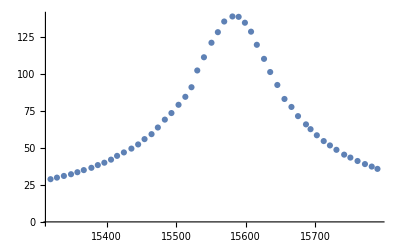

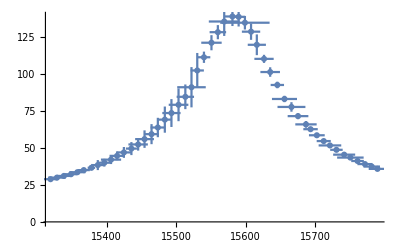

```mathematica
ErrorListPlot[errordata]
ErrorListPlot[errordata,ErrorBarFunction->ErrorBarScale[100,10]]
```